```mathematica
NS["samples_uniform_notuniform","C:\\Users\\pglpm\\repositories\\neurobayes"]
```

```mathematica
nout=10;
out=Range[1,nout];
unifp=Table[1,nout]/nout;
```

```mathematica
n=100;
nsamples=1000;
SeedRandom[666];

(* samples from uniform *)
samplesu=Table[(Count[RandomChoice[unifp->out,n],#]&/@out[[;;1]])/n,nsamples];

samplesd=
Table[(Count[RandomChoice[
(Append[#,1-Total@#]&@Flatten[RandomVariate[DirichletDistribution[Table[1,nout]],1]])->out,n],#]&/@out[[;;1]])/n,nsamples];
```

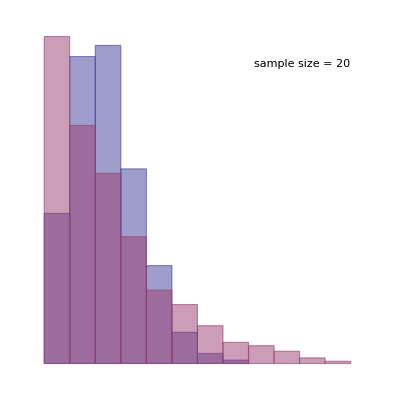

```mathematica
Histogram[{Flatten@samplesu,Flatten@samplesd},"Knuth","PDF",AspectRatio->1,PlotRange->{{-0.04,0.6},All},ImageSize->a4shortside/3*2,Epilog->Text["sample size = "<>ToString[n],Scaled[{0.8,0.9}]]]
```

```mathematica
expng["overlap_unif_all_n20",%]
```

overlap_unif_all_n20.png

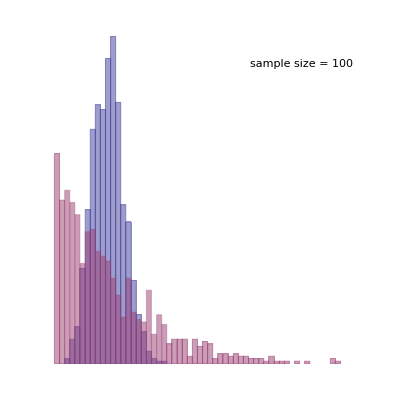

```mathematica
Histogram[{Flatten@samplesu,Flatten@samplesd},"Knuth","PDF",AspectRatio->1,PlotRange->{{-0.04,0.6},All},ImageSize->a4shortside/3*2,Epilog->Text["sample size = "<>ToString[n],Scaled[{0.8,0.9}]]]
```

```mathematica
expng["overlap_unif_all_n100",%]
```

overlap_unif_all_n100.png